```mathematica
coarse[matrix_,NN1_,NN2_]:=Module[{out},
out=Select[matrix,Mod[#[[1]],NN1]==0&&Mod[#[[2]],NN2]==0&];

Return[out];
]
```

```mathematica
SetDirectory["C:\\Users\\Paolo\\Desktop\\EoS_Final"]
```

C:\Users\Paolo\Desktop\EoS_Final

### w = 0.25

#### w = 0.25 --- rho = 0.5

```mathematica
Pressw025rho05=Import["Files_PAR_143_350_3_93_35_17\\Press_Final_PAR_143_350_3_93_35_17_3D.dat"];
```

```mathematica
Entrw025rho05=Import["Files_PAR_143_350_3_93_35_17\\Entr_Final_PAR_143_350_3_93_35_17_3D.dat"];
```

```mathematica
BarDensw025rho05=Import["Files_PAR_143_350_3_93_35_17\\BarDens_Final_PAR_143_350_3_93_35_17_3D.dat"];
```

```mathematica
EnerDensw025rho05=Import["Files_PAR_143_350_3_93_35_17\\EnerDens_Final_PAR_143_350_3_93_35_17_3D.dat"];
```

```mathematica
SpSoundw025rho05=Import["Files_PAR_143_350_3_93_35_17\\SpSound_Final_PAR_143_350_3_93_35_17_3D.dat"];
```

```mathematica
Select[Pressw025rho05,#[[3]]<0&]//Length
Select[Entrw025rho05,#[[3]]<0&]//Length
Select[BarDensw025rho05,#[[3]]<0&]//Length
Select[EnerDensw025rho05,#[[3]]<0&]//Length
Select[SpSoundw025rho05,#[[3]]<0&]//Length
```

0

5390

28695

36

4302

```mathematica
ListPlot3D[coarse[BarDensw025rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho05,Entrw025rho05,BarDensw025rho05,EnerDensw025rho05,SpSoundw025rho05]
```

#### w = 0.25 --- rho = 1.0

```mathematica
Pressw025rho1=Import["Files_PAR_143_350_3_93_35_35\\Press_Final_PAR_143_350_3_93_35_35_3D.dat"];
```

```mathematica
Entrw025rho1=Import["Files_PAR_143_350_3_93_35_35\\Entr_Final_PAR_143_350_3_93_35_35_3D.dat"];
```

```mathematica
BarDensw025rho1=Import["Files_PAR_143_350_3_93_35_35\\BarDens_Final_PAR_143_350_3_93_35_35_3D.dat"];
```

```mathematica
EnerDensw025rho1=Import["Files_PAR_143_350_3_93_35_35\\EnerDens_Final_PAR_143_350_3_93_35_35_3D.dat"];
```

```mathematica
SpSoundw025rho1=Import["Files_PAR_143_350_3_93_35_35\\SpSound_Final_PAR_143_350_3_93_35_35_3D.dat"];
```

```mathematica
Select[Pressw025rho1,#[[3]]<0&]//Length
Select[Entrw025rho1,#[[3]]<0&]//Length
Select[BarDensw025rho1,#[[3]]<0&]//Length
Select[EnerDensw025rho1,#[[3]]<0&]//Length
Select[SpSoundw025rho1,#[[3]]<0&]//Length
```

0

1870

5662

0

1845

```mathematica
ListPlot3D[
coarse[BarDensw025rho1,10,10]]
```

```mathematica
ListPlot3D[
coarse[SpSoundw025rho1,10,10]]
```

```mathematica
Clear[Pressw025rho1,Entrw025rho1,BarDensw025rho1,EnerDensw025rho1,SpSoundw025rho1]
```

#### w = 0.25 --- rho = 1.5

```mathematica
Pressw025rho15=Import["Files_PAR_143_350_3_93_35_53\\Press_Final_PAR_143_350_3_93_35_53_3D.dat"];
```

```mathematica
Entrw025rho15=Import["Files_PAR_143_350_3_93_35_53\\Entr_Final_PAR_143_350_3_93_35_53_3D.dat"];
```

```mathematica
BarDensw025rho15=Import["Files_PAR_143_350_3_93_35_53\\BarDens_Final_PAR_143_350_3_93_35_53_3D.dat"];
```

```mathematica
EnerDensw025rho15=Import["Files_PAR_143_350_3_93_35_53\\EnerDens_Final_PAR_143_350_3_93_35_53_3D.dat"];
```

```mathematica
SpSoundw025rho15=Import["Files_PAR_143_350_3_93_35_53\\SpSound_Final_PAR_143_350_3_93_35_53_3D.dat"];
```

```mathematica
Select[Pressw025rho15,#[[3]]<0&]//Length
Select[Entrw025rho15,#[[3]]<0&]//Length
Select[BarDensw025rho15,#[[3]]<0&]//Length
Select[EnerDensw025rho15,#[[3]]<0&]//Length
Select[SpSoundw025rho15,#[[3]]<0&]//Length
```

0

0

7056

0

590

```mathematica
ListPlot3D[coarse[BarDensw025rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho15,Entrw025rho15,BarDensw025rho15,EnerDensw025rho15,SpSoundw025rho15]
```

#### w = 0.25 --- rho = 2.0

```mathematica
Pressw025rho2=Import["Files_PAR_143_350_3_93_35_71\\Press_Final_PAR_143_350_3_93_35_71_3D.dat"];
```

```mathematica
Entrw025rho2=Import["Files_PAR_143_350_3_93_35_71\\Entr_Final_PAR_143_350_3_93_35_71_3D.dat"];
```

```mathematica
BarDensw025rho2=Import["Files_PAR_143_350_3_93_35_71\\BarDens_Final_PAR_143_350_3_93_35_71_3D.dat"];
```

```mathematica
EnerDensw025rho2=Import["Files_PAR_143_350_3_93_35_71\\EnerDens_Final_PAR_143_350_3_93_35_71_3D.dat"];
```

```mathematica
SpSoundw025rho2=Import["Files_PAR_143_350_3_93_35_71\\SpSound_Final_PAR_143_350_3_93_35_71_3D.dat"];
```

```mathematica
Select[Pressw025rho2,#[[3]]<0&]//Length
Select[Entrw025rho2,#[[3]]<0&]//Length
Select[BarDensw025rho2,#[[3]]<0&]//Length
Select[EnerDensw025rho2,#[[3]]<0&]//Length
Select[SpSoundw025rho2,#[[3]]<0&]//Length
```

0

0

6814

0

504

```mathematica
ListPlot3D[coarse[BarDensw025rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho2,Entrw025rho2,BarDensw025rho2,EnerDensw025rho2,SpSoundw025rho2]
```

#### w = 0.25 --- rho = 2.5

```mathematica
Pressw025rho25=Import["Files_PAR_143_350_3_93_35_89\\Press_Final_PAR_143_350_3_93_35_89_3D.dat"];
```

```mathematica
Entrw025rho25=Import["Files_PAR_143_350_3_93_35_89\\Entr_Final_PAR_143_350_3_93_35_89_3D.dat"];
```

```mathematica
BarDensw025rho25=Import["Files_PAR_143_350_3_93_35_89\\BarDens_Final_PAR_143_350_3_93_35_89_3D.dat"];
```

```mathematica
EnerDensw025rho25=Import["Files_PAR_143_350_3_93_35_89\\EnerDens_Final_PAR_143_350_3_93_35_89_3D.dat"];
```

```mathematica
SpSoundw025rho25=Import["Files_PAR_143_350_3_93_35_89\\SpSound_Final_PAR_143_350_3_93_35_89_3D.dat"];
```

```mathematica
Select[Pressw025rho25,#[[3]]<0&]//Length
Select[Entrw025rho25,#[[3]]<0&]//Length
Select[BarDensw025rho25,#[[3]]<0&]//Length
Select[EnerDensw025rho25,#[[3]]<0&]//Length
Select[SpSoundw025rho25,#[[3]]<0&]//Length
```

0

0

3709

0

633

```mathematica
ListPlot3D[coarse[BarDensw025rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho25,Entrw025rho25,BarDensw025rho25,EnerDensw025rho25,SpSoundw025rho25]
```

#### w = 0.25 --- rho = 3.0

```mathematica
Pressw025rho3=Import["Files_PAR_143_350_3_93_35_107\\Press_Final_PAR_143_350_3_93_35_107_3D.dat"];
```

```mathematica
Entrw025rho3=Import["Files_PAR_143_350_3_93_35_107\\Entr_Final_PAR_143_350_3_93_35_107_3D.dat"];
```

```mathematica
BarDensw025rho3=Import["Files_PAR_143_350_3_93_35_107\\BarDens_Final_PAR_143_350_3_93_35_107_3D.dat"];
```

```mathematica
EnerDensw025rho3=Import["Files_PAR_143_350_3_93_35_107\\EnerDens_Final_PAR_143_350_3_93_35_107_3D.dat"];
```

```mathematica
SpSoundw025rho3=Import["Files_PAR_143_350_3_93_35_107\\SpSound_Final_PAR_143_350_3_93_35_107_3D.dat"];
```

```mathematica
Select[Pressw025rho3,#[[3]]<0&]//Length
Select[Entrw025rho3,#[[3]]<0&]//Length
Select[BarDensw025rho3,#[[3]]<0&]//Length
Select[EnerDensw025rho3,#[[3]]<0&]//Length
Select[SpSoundw025rho3,#[[3]]<0&]//Length
```

0

0

1760

0

510

```mathematica
ListPlot3D[coarse[BarDensw025rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho3,Entrw025rho3,BarDensw025rho3,EnerDensw025rho3,SpSoundw025rho3]
```

#### w = 0.25 --- rho = 3.5

```mathematica
Pressw025rho35=Import["Files_PAR_143_350_3_93_35_125\\Press_Final_PAR_143_350_3_93_35_125_3D.dat"];
```

```mathematica
Entrw025rho35=Import["Files_PAR_143_350_3_93_35_125\\Entr_Final_PAR_143_350_3_93_35_125_3D.dat"];
```

```mathematica
BarDensw025rho35=Import["Files_PAR_143_350_3_93_35_125\\BarDens_Final_PAR_143_350_3_93_35_125_3D.dat"];
```

```mathematica
EnerDensw025rho35=Import["Files_PAR_143_350_3_93_35_125\\EnerDens_Final_PAR_143_350_3_93_35_125_3D.dat"];
```

```mathematica
SpSoundw025rho35=Import["Files_PAR_143_350_3_93_35_125\\SpSound_Final_PAR_143_350_3_93_35_125_3D.dat"];
```

```mathematica
Select[Pressw025rho35,#[[3]]<0&]//Length
Select[Entrw025rho35,#[[3]]<0&]//Length
Select[BarDensw025rho35,#[[3]]<0&]//Length
Select[EnerDensw025rho35,#[[3]]<0&]//Length
Select[SpSoundw025rho35,#[[3]]<0&]//Length
```

0

0

989

0

429

```mathematica
ListPlot3D[coarse[BarDensw025rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho35,Entrw025rho35,BarDensw025rho35,EnerDensw025rho35,SpSoundw025rho35]
```

#### w = 0.25 --- rho = 4.0

```mathematica
Pressw025rho4=Import["Files_PAR_143_350_3_93_35_143\\Press_Final_PAR_143_350_3_93_35_143_3D.dat"];
```

```mathematica
Entrw025rho4=Import["Files_PAR_143_350_3_93_35_143\\Entr_Final_PAR_143_350_3_93_35_143_3D.dat"];
```

```mathematica
BarDensw025rho4=Import["Files_PAR_143_350_3_93_35_143\\BarDens_Final_PAR_143_350_3_93_35_143_3D.dat"];
```

```mathematica
EnerDensw025rho4=Import["Files_PAR_143_350_3_93_35_143\\EnerDens_Final_PAR_143_350_3_93_35_143_3D.dat"];
```

```mathematica
SpSoundw025rho4=Import["Files_PAR_143_350_3_93_35_143\\SpSound_Final_PAR_143_350_3_93_35_143_3D.dat"];
```

```mathematica
Select[Pressw025rho4,#[[3]]<0&]//Length
Select[Entrw025rho4,#[[3]]<0&]//Length
Select[BarDensw025rho4,#[[3]]<0&]//Length
Select[EnerDensw025rho4,#[[3]]<0&]//Length
Select[SpSoundw025rho4,#[[3]]<0&]//Length
```

0

0

720

0

358

```mathematica
ListPlot3D[coarse[BarDensw025rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw025rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw025rho4,Entrw025rho4,BarDensw025rho4,EnerDensw025rho4,SpSoundw025rho4]
```

### w = 0.50

#### w = 0.50 --- rho = 0.5

```mathematica
Pressw05rho05=Import["Files_PAR_143_350_3_93_71_35\\Press_Final_PAR_143_350_3_93_71_35_3D.dat"];
```

```mathematica
Entrw05rho05=Import["Files_PAR_143_350_3_93_71_35\\Entr_Final_PAR_143_350_3_93_71_35_3D.dat"];
```

```mathematica
BarDensw05rho05=Import["Files_PAR_143_350_3_93_71_35\\BarDens_Final_PAR_143_350_3_93_71_35_3D.dat"];
```

```mathematica
EnerDensw05rho05=Import["Files_PAR_143_350_3_93_71_35\\EnerDens_Final_PAR_143_350_3_93_71_35_3D.dat"];
```

```mathematica
SpSoundw05rho05=Import["Files_PAR_143_350_3_93_71_35\\SpSound_Final_PAR_143_350_3_93_71_35_3D.dat"];
```

```mathematica
Select[Pressw05rho05,#[[3]]<0&]//Length
Select[Entrw05rho05,#[[3]]<0&]//Length
Select[BarDensw05rho05,#[[3]]<0&]//Length
Select[EnerDensw05rho05,#[[3]]<0&]//Length
Select[SpSoundw05rho05,#[[3]]<0&]//Length
```

0

1880

5808

0

1699

```mathematica
ListPlot3D[coarse[BarDensw05rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho05,Entrw05rho05,BarDensw05rho05,EnerDensw05rho05,SpSoundw05rho05]
```

#### w = 0.50 --- rho = 1.0

```mathematica
Pressw05rho1=Import["Files_PAR_143_350_3_93_71_71\\Press_Final_PAR_143_350_3_93_71_71_3D.dat"];
```

```mathematica
Entrw05rho1=Import["Files_PAR_143_350_3_93_71_71\\Entr_Final_PAR_143_350_3_93_71_71_3D.dat"];
```

```mathematica
BarDensw05rho1=Import["Files_PAR_143_350_3_93_71_71\\BarDens_Final_PAR_143_350_3_93_71_71_3D.dat"];
```

```mathematica
EnerDensw05rho1=Import["Files_PAR_143_350_3_93_71_71\\EnerDens_Final_PAR_143_350_3_93_71_71_3D.dat"];
```

```mathematica
SpSoundw05rho1=Import["Files_PAR_143_350_3_93_71_71\\SpSound_Final_PAR_143_350_3_93_71_71_3D.dat"];
```

```mathematica
Select[Pressw05rho1,#[[3]]<0&]//Length
Select[Entrw05rho1,#[[3]]<0&]//Length
Select[BarDensw05rho1,#[[3]]<0&]//Length
Select[EnerDensw05rho1,#[[3]]<0&]//Length
Select[SpSoundw05rho1,#[[3]]<0&]//Length
```

0

0

3061

0

15

```mathematica
ListPlot3D[coarse[BarDensw05rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho1,Entrw05rho1,BarDensw05rho1,EnerDensw05rho1,SpSoundw05rho1]
```

#### w = 0.50 --- rho = 1.5

```mathematica
Pressw05rho15=Import["Files_PAR_143_350_3_93_71_107\\Press_Final_PAR_143_350_3_93_71_107_3D.dat"];
```

```mathematica
Entrw05rho15=Import["Files_PAR_143_350_3_93_71_107\\Entr_Final_PAR_143_350_3_93_71_107_3D.dat"];
```

```mathematica
BarDensw05rho15=Import["Files_PAR_143_350_3_93_71_107\\BarDens_Final_PAR_143_350_3_93_71_107_3D.dat"];
```

```mathematica
EnerDensw05rho15=Import["Files_PAR_143_350_3_93_71_107\\EnerDens_Final_PAR_143_350_3_93_71_107_3D.dat"];
```

```mathematica
SpSoundw05rho15=Import["Files_PAR_143_350_3_93_71_107\\SpSound_Final_PAR_143_350_3_93_71_107_3D.dat"];
```

```mathematica
Select[Pressw05rho15,#[[3]]<0&]//Length
Select[Entrw05rho15,#[[3]]<0&]//Length
Select[BarDensw05rho15,#[[3]]<0&]//Length
Select[EnerDensw05rho15,#[[3]]<0&]//Length
Select[SpSoundw05rho15,#[[3]]<0&]//Length
```

0

0

3232

0

104

```mathematica
ListPlot3D[coarse[BarDensw05rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho15,Entrw05rho15,BarDensw05rho15,EnerDensw05rho15,SpSoundw05rho15]
```

#### w = 0.50 --- rho = 2.0

```mathematica
Pressw05rho2=Import["Files_PAR_143_350_3_93_71_143\\Press_Final_PAR_143_350_3_93_71_143_3D.dat"];
```

```mathematica
Entrw05rho2=Import["Files_PAR_143_350_3_93_71_143\\Entr_Final_PAR_143_350_3_93_71_143_3D.dat"];
```

```mathematica
BarDensw05rho2=Import["Files_PAR_143_350_3_93_71_143\\BarDens_Final_PAR_143_350_3_93_71_143_3D.dat"];
```

```mathematica
EnerDensw05rho2=Import["Files_PAR_143_350_3_93_71_143\\EnerDens_Final_PAR_143_350_3_93_71_143_3D.dat"];
```

```mathematica
SpSoundw05rho2=Import["Files_PAR_143_350_3_93_71_143\\SpSound_Final_PAR_143_350_3_93_71_143_3D.dat"];
```

```mathematica
Select[Pressw05rho2,#[[3]]<0&]//Length
Select[Entrw05rho2,#[[3]]<0&]//Length
Select[BarDensw05rho2,#[[3]]<0&]//Length
Select[EnerDensw05rho2,#[[3]]<0&]//Length
Select[SpSoundw05rho2,#[[3]]<0&]//Length
```

0

0

1152

0

49

```mathematica
ListPlot3D[coarse[BarDensw05rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho2,Entrw05rho2,BarDensw05rho2,EnerDensw05rho2,SpSoundw05rho2]
```

#### w = 0.50 --- rho = 2.5

```mathematica
Pressw05rho25=Import["Files_PAR_143_350_3_93_71_179\\Press_Final_PAR_143_350_3_93_71_179_3D.dat"];
```

```mathematica
Entrw05rho25=Import["Files_PAR_143_350_3_93_71_179\\Entr_Final_PAR_143_350_3_93_71_179_3D.dat"];
```

```mathematica
BarDensw05rho25=Import["Files_PAR_143_350_3_93_71_179\\BarDens_Final_PAR_143_350_3_93_71_179_3D.dat"];
```

```mathematica
EnerDensw05rho25=Import["Files_PAR_143_350_3_93_71_179\\EnerDens_Final_PAR_143_350_3_93_71_179_3D.dat"];
```

```mathematica
SpSoundw05rho25=Import["Files_PAR_143_350_3_93_71_179\\SpSound_Final_PAR_143_350_3_93_71_179_3D.dat"];
```

```mathematica
Select[Pressw05rho25,#[[3]]<0&]//Length
Select[Entrw05rho25,#[[3]]<0&]//Length
Select[BarDensw05rho25,#[[3]]<0&]//Length
Select[EnerDensw05rho25,#[[3]]<0&]//Length
Select[SpSoundw05rho25,#[[3]]<0&]//Length
```

0

0

364

0

1

```mathematica
ListPlot3D[coarse[BarDensw05rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho25,Entrw05rho25,BarDensw05rho25,EnerDensw05rho25,SpSoundw05rho25]
```

#### w = 0.50 --- rho = 3.0

```mathematica
Pressw05rho3=Import["Files_PAR_143_350_3_93_71_214\\Press_Final_PAR_143_350_3_93_71_214_3D.dat"];
```

```mathematica
Entrw05rho3=Import["Files_PAR_143_350_3_93_71_214\\Entr_Final_PAR_143_350_3_93_71_214_3D.dat"];
```

```mathematica
BarDensw05rho3=Import["Files_PAR_143_350_3_93_71_214\\BarDens_Final_PAR_143_350_3_93_71_214_3D.dat"];
```

```mathematica
EnerDensw05rho3=Import["Files_PAR_143_350_3_93_71_214\\EnerDens_Final_PAR_143_350_3_93_71_214_3D.dat"];
```

```mathematica
SpSoundw05rho3=Import["Files_PAR_143_350_3_93_71_214\\SpSound_Final_PAR_143_350_3_93_71_214_3D.dat"];
```

```mathematica
Select[Pressw05rho3,#[[3]]<0&]//Length
Select[Entrw05rho3,#[[3]]<0&]//Length
Select[BarDensw05rho3,#[[3]]<0&]//Length
Select[EnerDensw05rho3,#[[3]]<0&]//Length
Select[SpSoundw05rho3,#[[3]]<0&]//Length
```

0

0

209

0

0

```mathematica
ListPlot3D[coarse[BarDensw05rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho3,Entrw05rho3,BarDensw05rho3,EnerDensw05rho3,SpSoundw05rho3]
```

#### w = 0.50 --- rho = 3.5

```mathematica
Pressw05rho35=Import["Files_PAR_143_350_3_93_71_250\\Press_Final_PAR_143_350_3_93_71_250_3D.dat"];
```

```mathematica
Entrw05rho35=Import["Files_PAR_143_350_3_93_71_250\\Entr_Final_PAR_143_350_3_93_71_250_3D.dat"];
```

```mathematica
BarDensw05rho35=Import["Files_PAR_143_350_3_93_71_250\\BarDens_Final_PAR_143_350_3_93_71_250_3D.dat"];
```

```mathematica
EnerDensw05rho35=Import["Files_PAR_143_350_3_93_71_250\\EnerDens_Final_PAR_143_350_3_93_71_250_3D.dat"];
```

```mathematica
SpSoundw05rho35=Import["Files_PAR_143_350_3_93_71_250\\SpSound_Final_PAR_143_350_3_93_71_250_3D.dat"];
```

```mathematica
Select[Pressw05rho35,#[[3]]<0&]//Length
Select[Entrw05rho35,#[[3]]<0&]//Length
Select[BarDensw05rho35,#[[3]]<0&]//Length
Select[EnerDensw05rho35,#[[3]]<0&]//Length
Select[SpSoundw05rho35,#[[3]]<0&]//Length
```

0

0

144

0

0

```mathematica
ListPlot3D[coarse[BarDensw05rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho35,Entrw05rho35,BarDensw05rho35,EnerDensw05rho35,SpSoundw05rho35]
```

#### w = 0.50 --- rho = 4.0

```mathematica
Pressw05rho4=Import["Files_PAR_143_350_3_93_71_286\\Press_Final_PAR_143_350_3_93_71_286_3D.dat"];
```

```mathematica
Entrw05rho4=Import["Files_PAR_143_350_3_93_71_286\\Entr_Final_PAR_143_350_3_93_71_286_3D.dat"];
```

```mathematica
BarDensw05rho4=Import["Files_PAR_143_350_3_93_71_286\\BarDens_Final_PAR_143_350_3_93_71_286_3D.dat"];
```

```mathematica
EnerDensw05rho4=Import["Files_PAR_143_350_3_93_71_286\\EnerDens_Final_PAR_143_350_3_93_71_286_3D.dat"];
```

```mathematica
SpSoundw05rho4=Import["Files_PAR_143_350_3_93_71_286\\SpSound_Final_PAR_143_350_3_93_71_286_3D.dat"];
```

```mathematica
Select[Pressw05rho4,#[[3]]<0&]//Length
Select[Entrw05rho4,#[[3]]<0&]//Length
Select[BarDensw05rho4,#[[3]]<0&]//Length
Select[EnerDensw05rho4,#[[3]]<0&]//Length
Select[SpSoundw05rho4,#[[3]]<0&]//Length
```

0

0

103

0

0

```mathematica
ListPlot3D[coarse[BarDensw05rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw05rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw05rho4,Entrw05rho4,BarDensw05rho4,EnerDensw05rho4,SpSoundw05rho4]
```

### w = 0.75

#### w = 0.75 --- rho = 0.5

```mathematica
Pressw075rho05=Import["Files_PAR_143_350_3_93_107_53\\Press_Final_PAR_143_350_3_93_107_53_3D.dat"];
```

```mathematica
Entrw075rho05=Import["Files_PAR_143_350_3_93_107_53\\Entr_Final_PAR_143_350_3_93_107_53_3D.dat"];
```

```mathematica
BarDensw075rho05=Import["Files_PAR_143_350_3_93_107_53\\BarDens_Final_PAR_143_350_3_93_107_53_3D.dat"];
```

```mathematica
EnerDensw075rho05=Import["Files_PAR_143_350_3_93_107_53\\EnerDens_Final_PAR_143_350_3_93_107_53_3D.dat"];
```

```mathematica
SpSoundw075rho05=Import["Files_PAR_143_350_3_93_107_53\\SpSound_Final_PAR_143_350_3_93_107_53_3D.dat"];
```

```mathematica
Select[Pressw075rho05,#[[3]]<0&]//Length
Select[Entrw075rho05,#[[3]]<0&]//Length
Select[BarDensw075rho05,#[[3]]<0&]//Length
Select[EnerDensw075rho05,#[[3]]<0&]//Length
Select[SpSoundw075rho05,#[[3]]<0&]//Length
```

0

300

2956

0

298

```mathematica
ListPlot3D[coarse[BarDensw075rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho05,Entrw075rho05,BarDensw075rho05,EnerDensw075rho05,SpSoundw075rho05]
```

#### w = 0.75 --- rho = 1.0

```mathematica
Pressw075rho1=Import["Files_PAR_143_350_3_93_107_107\\Press_Final_PAR_143_350_3_93_107_107_3D.dat"];
```

```mathematica
Entrw075rho1=Import["Files_PAR_143_350_3_93_107_107\\Entr_Final_PAR_143_350_3_93_107_107_3D.dat"];
```

```mathematica
BarDensw075rho1=Import["Files_PAR_143_350_3_93_107_107\\BarDens_Final_PAR_143_350_3_93_107_107_3D.dat"];
```

```mathematica
EnerDensw075rho1=Import["Files_PAR_143_350_3_93_107_107\\EnerDens_Final_PAR_143_350_3_93_107_107_3D.dat"];
```

```mathematica
SpSoundw075rho1=Import["Files_PAR_143_350_3_93_107_107\\SpSound_Final_PAR_143_350_3_93_107_107_3D.dat"];
```

```mathematica
Select[Pressw075rho1,#[[3]]<0&]//Length
Select[Entrw075rho1,#[[3]]<0&]//Length
Select[BarDensw075rho1,#[[3]]<0&]//Length
Select[EnerDensw075rho1,#[[3]]<0&]//Length
Select[SpSoundw075rho1,#[[3]]<0&]//Length
```

0

0

2494

0

33

```mathematica
ListPlot3D[coarse[BarDensw075rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho1,Entrw075rho1,BarDensw075rho1,EnerDensw075rho1,SpSoundw075rho1]
```

#### w = 0.75 --- rho = 1.5

```mathematica
Pressw075rho15=Import["Files_PAR_143_350_3_93_107_161\\Press_Final_PAR_143_350_3_93_107_161_3D.dat"];
```

```mathematica
Entrw075rho15=Import["Files_PAR_143_350_3_93_107_161\\Entr_Final_PAR_143_350_3_93_107_161_3D.dat"];
```

```mathematica
BarDensw075rho15=Import["Files_PAR_143_350_3_93_107_161\\BarDens_Final_PAR_143_350_3_93_107_161_3D.dat"];
```

```mathematica
EnerDensw075rho15=Import["Files_PAR_143_350_3_93_107_161\\EnerDens_Final_PAR_143_350_3_93_107_161_3D.dat"];
```

```mathematica
SpSoundw075rho15=Import["Files_PAR_143_350_3_93_107_161\\SpSound_Final_PAR_143_350_3_93_107_161_3D.dat"];
```

```mathematica
Select[Pressw075rho15,#[[3]]<0&]//Length
Select[Entrw075rho15,#[[3]]<0&]//Length
Select[BarDensw075rho15,#[[3]]<0&]//Length
Select[EnerDensw075rho15,#[[3]]<0&]//Length
Select[SpSoundw075rho15,#[[3]]<0&]//Length
```

0

0

1249

0

15

```mathematica
ListPlot3D[coarse[BarDensw075rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho15,Entrw075rho15,BarDensw075rho15,EnerDensw075rho15,SpSoundw075rho15]
```

#### w = 0.75 --- rho = 2.0

```mathematica
Pressw075rho2=Import["Files_PAR_143_350_3_93_107_214\\Press_Final_PAR_143_350_3_93_107_214_3D.dat"];
```

```mathematica
Entrw075rho2=Import["Files_PAR_143_350_3_93_107_214\\Entr_Final_PAR_143_350_3_93_107_214_3D.dat"];
```

```mathematica
BarDensw075rho2=Import["Files_PAR_143_350_3_93_107_214\\BarDens_Final_PAR_143_350_3_93_107_214_3D.dat"];
```

```mathematica
EnerDensw075rho2=Import["Files_PAR_143_350_3_93_107_214\\EnerDens_Final_PAR_143_350_3_93_107_214_3D.dat"];
```

```mathematica
SpSoundw075rho2=Import["Files_PAR_143_350_3_93_107_214\\SpSound_Final_PAR_143_350_3_93_107_214_3D.dat"];
```

```mathematica
Select[Pressw075rho2,#[[3]]<0&]//Length
Select[Entrw075rho2,#[[3]]<0&]//Length
Select[BarDensw075rho2,#[[3]]<0&]//Length
Select[EnerDensw075rho2,#[[3]]<0&]//Length
Select[SpSoundw075rho2,#[[3]]<0&]//Length
```

0

0

214

0

1

```mathematica
ListPlot3D[coarse[BarDensw075rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho2,Entrw075rho2,BarDensw075rho2,EnerDensw075rho2,SpSoundw075rho2]
```

#### w = 0.75 --- rho = 2.5

```mathematica
Pressw075rho25=Import["Files_PAR_143_350_3_93_107_268\\Press_Final_PAR_143_350_3_93_107_268_3D.dat"];
```

```mathematica
Entrw075rho25=Import["Files_PAR_143_350_3_93_107_268\\Entr_Final_PAR_143_350_3_93_107_268_3D.dat"];
```

```mathematica
BarDensw075rho25=Import["Files_PAR_143_350_3_93_107_268\\BarDens_Final_PAR_143_350_3_93_107_268_3D.dat"];
```

```mathematica
EnerDensw075rho25=Import["Files_PAR_143_350_3_93_107_268\\EnerDens_Final_PAR_143_350_3_93_107_268_3D.dat"];
```

```mathematica
SpSoundw075rho25=Import["Files_PAR_143_350_3_93_107_268\\SpSound_Final_PAR_143_350_3_93_107_268_3D.dat"];
```

```mathematica
Select[Pressw075rho25,#[[3]]<0&]//Length
Select[Entrw075rho25,#[[3]]<0&]//Length
Select[BarDensw075rho25,#[[3]]<0&]//Length
Select[EnerDensw075rho25,#[[3]]<0&]//Length
Select[SpSoundw075rho25,#[[3]]<0&]//Length
```

0

0

115

0

0

```mathematica
ListPlot3D[coarse[BarDensw075rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho25,Entrw075rho25,BarDensw075rho25,EnerDensw075rho25,SpSoundw075rho25]
```

#### w = 0.75 --- rho = 3.0

```mathematica
Pressw075rho3=Import["Files_PAR_143_350_3_93_107_322\\Press_Final_PAR_143_350_3_93_107_322_3D.dat"];
```

```mathematica
Entrw075rho3=Import["Files_PAR_143_350_3_93_107_322\\Entr_Final_PAR_143_350_3_93_107_322_3D.dat"];
```

```mathematica
BarDensw075rho3=Import["Files_PAR_143_350_3_93_107_322\\BarDens_Final_PAR_143_350_3_93_107_322_3D.dat"];
```

```mathematica
EnerDensw075rho3=Import["Files_PAR_143_350_3_93_107_322\\EnerDens_Final_PAR_143_350_3_93_107_322_3D.dat"];
```

```mathematica
SpSoundw075rho3=Import["Files_PAR_143_350_3_93_107_322\\SpSound_Final_PAR_143_350_3_93_107_322_3D.dat"];
```

```mathematica
Select[Pressw075rho3,#[[3]]<0&]//Length
Select[Entrw075rho3,#[[3]]<0&]//Length
Select[BarDensw075rho3,#[[3]]<0&]//Length
Select[EnerDensw075rho3,#[[3]]<0&]//Length
Select[SpSoundw075rho3,#[[3]]<0&]//Length
```

0

0

74

0

0

```mathematica
ListPlot3D[coarse[BarDensw075rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho3,Entrw075rho3,BarDensw075rho3,EnerDensw075rho3,SpSoundw075rho3]
```

#### w = 0.75 --- rho = 3.5

```mathematica
Pressw075rho35=Import["Files_PAR_143_350_3_93_107_375\\Press_Final_PAR_143_350_3_93_107_375_3D.dat"];
```

```mathematica
Entrw075rho35=Import["Files_PAR_143_350_3_93_107_375\\Entr_Final_PAR_143_350_3_93_107_375_3D.dat"];
```

```mathematica
BarDensw075rho35=Import["Files_PAR_143_350_3_93_107_375\\BarDens_Final_PAR_143_350_3_93_107_375_3D.dat"];
```

```mathematica
EnerDensw075rho35=Import["Files_PAR_143_350_3_93_107_375\\EnerDens_Final_PAR_143_350_3_93_107_375_3D.dat"];
```

```mathematica
SpSoundw075rho35=Import["Files_PAR_143_350_3_93_107_375\\SpSound_Final_PAR_143_350_3_93_107_375_3D.dat"];
```

```mathematica
Select[Pressw075rho35,#[[3]]<0&]//Length
Select[Entrw075rho35,#[[3]]<0&]//Length
Select[BarDensw075rho35,#[[3]]<0&]//Length
Select[EnerDensw075rho35,#[[3]]<0&]//Length
Select[SpSoundw075rho35,#[[3]]<0&]//Length
```

0

0

49

0

0

```mathematica
ListPlot3D[coarse[BarDensw075rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho35,Entrw075rho35,BarDensw075rho35,EnerDensw075rho35,SpSoundw075rho35]
```

#### w = 0.75 --- rho = 4.0

```mathematica
Pressw075rho4=Import["Files_PAR_143_350_3_93_107_429\\Press_Final_PAR_143_350_3_93_107_429_3D.dat"];
```

```mathematica
Entrw075rho4=Import["Files_PAR_143_350_3_93_107_429\\Entr_Final_PAR_143_350_3_93_107_429_3D.dat"];
```

```mathematica
BarDensw075rho4=Import["Files_PAR_143_350_3_93_107_429\\BarDens_Final_PAR_143_350_3_93_107_429_3D.dat"];
```

```mathematica
EnerDensw075rho4=Import["Files_PAR_143_350_3_93_107_429\\EnerDens_Final_PAR_143_350_3_93_107_429_3D.dat"];
```

```mathematica
SpSoundw075rho4=Import["Files_PAR_143_350_3_93_107_429\\SpSound_Final_PAR_143_350_3_93_107_429_3D.dat"];
```

```mathematica
Select[Pressw075rho4,#[[3]]<0&]//Length
Select[Entrw075rho4,#[[3]]<0&]//Length
Select[BarDensw075rho4,#[[3]]<0&]//Length
Select[EnerDensw075rho4,#[[3]]<0&]//Length
Select[SpSoundw075rho4,#[[3]]<0&]//Length
```

0

0

31

0

0

```mathematica
ListPlot3D[coarse[BarDensw075rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw075rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw075rho4,Entrw075rho4,BarDensw075rho4,EnerDensw075rho4,SpSoundw075rho4]
```

### w = 1.00

#### w = 1.00 --- rho = 0.5

```mathematica
Pressw1rho05=Import["Files_PAR_143_350_3_93_143_71\\Press_Final_PAR_143_350_3_93_143_71_3D.dat"];
```

```mathematica
Entrw1rho05=Import["Files_PAR_143_350_3_93_143_71\\Entr_Final_PAR_143_350_3_93_143_71_3D.dat"];
```

```mathematica
BarDensw1rho05=Import["Files_PAR_143_350_3_93_143_71\\BarDens_Final_PAR_143_350_3_93_143_71_3D.dat"];
```

```mathematica
EnerDensw1rho05=Import["Files_PAR_143_350_3_93_143_71\\EnerDens_Final_PAR_143_350_3_93_143_71_3D.dat"];
```

```mathematica
SpSoundw1rho05=Import["Files_PAR_143_350_3_93_143_71\\SpSound_Final_PAR_143_350_3_93_143_71_3D.dat"];
```

```mathematica
Select[Pressw1rho05,#[[3]]<0&]//Length
Select[Entrw1rho05,#[[3]]<0&]//Length
Select[BarDensw1rho05,#[[3]]<0&]//Length
Select[EnerDensw1rho05,#[[3]]<0&]//Length
Select[SpSoundw1rho05,#[[3]]<0&]//Length
```

0

0

1789

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho05,Entrw1rho05,BarDensw1rho05,EnerDensw1rho05,SpSoundw1rho05]
```

#### w = 1.00 --- rho = 1.0

```mathematica
Pressw1rho1=Import["Files_PAR_143_350_3_93_143_143\\Press_Final_PAR_143_350_3_93_143_143_3D.dat"];
```

```mathematica
Entrw1rho1=Import["Files_PAR_143_350_3_93_143_143\\Entr_Final_PAR_143_350_3_93_143_143_3D.dat"];
```

```mathematica
BarDensw1rho1=Import["Files_PAR_143_350_3_93_143_143\\BarDens_Final_PAR_143_350_3_93_143_143_3D.dat"];
```

```mathematica
EnerDensw1rho1=Import["Files_PAR_143_350_3_93_143_143\\EnerDens_Final_PAR_143_350_3_93_143_143_3D.dat"];
```

```mathematica
SpSoundw1rho1=Import["Files_PAR_143_350_3_93_143_143\\SpSound_Final_PAR_143_350_3_93_143_143_3D.dat"];
```

```mathematica
Select[Pressw1rho1,#[[3]]<0&]//Length
Select[Entrw1rho1,#[[3]]<0&]//Length
Select[BarDensw1rho1,#[[3]]<0&]//Length
Select[EnerDensw1rho1,#[[3]]<0&]//Length
Select[SpSoundw1rho1,#[[3]]<0&]//Length
```

0

0

1803

0

27

```mathematica
ListPlot3D[coarse[BarDensw1rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho1,Entrw1rho1,BarDensw1rho1,EnerDensw1rho1,SpSoundw1rho1]
```

#### w = 1.00 --- rho = 1.5

```mathematica
Pressw1rho15=Import["Files_PAR_143_350_3_93_143_214\\Press_Final_PAR_143_350_3_93_143_214_3D.dat"];
```

```mathematica
Entrw1rho15=Import["Files_PAR_143_350_3_93_143_214\\Entr_Final_PAR_143_350_3_93_143_214_3D.dat"];
```

```mathematica
BarDensw1rho15=Import["Files_PAR_143_350_3_93_143_214\\BarDens_Final_PAR_143_350_3_93_143_214_3D.dat"];
```

```mathematica
EnerDensw1rho15=Import["Files_PAR_143_350_3_93_143_214\\EnerDens_Final_PAR_143_350_3_93_143_214_3D.dat"];
```

```mathematica
SpSoundw1rho15=Import["Files_PAR_143_350_3_93_143_214\\SpSound_Final_PAR_143_350_3_93_143_214_3D.dat"];
```

```mathematica
Select[Pressw1rho15,#[[3]]<0&]//Length
Select[Entrw1rho15,#[[3]]<0&]//Length
Select[BarDensw1rho15,#[[3]]<0&]//Length
Select[EnerDensw1rho15,#[[3]]<0&]//Length
Select[SpSoundw1rho15,#[[3]]<0&]//Length
```

0

0

410

0

2

```mathematica
ListPlot3D[coarse[BarDensw1rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho15,Entrw1rho15,BarDensw1rho15,EnerDensw1rho15,SpSoundw1rho15]
```

#### w = 1.00 --- rho = 2.0

```mathematica
Pressw1rho2=Import["Files_PAR_143_350_3_93_143_286\\Press_Final_PAR_143_350_3_93_143_286_3D.dat"];
```

```mathematica
Entrw1rho2=Import["Files_PAR_143_350_3_93_143_286\\Entr_Final_PAR_143_350_3_93_143_286_3D.dat"];
```

```mathematica
BarDensw1rho2=Import["Files_PAR_143_350_3_93_143_286\\BarDens_Final_PAR_143_350_3_93_143_286_3D.dat"];
```

```mathematica
EnerDensw1rho2=Import["Files_PAR_143_350_3_93_143_286\\EnerDens_Final_PAR_143_350_3_93_143_286_3D.dat"];
```

```mathematica
SpSoundw1rho2=Import["Files_PAR_143_350_3_93_143_286\\SpSound_Final_PAR_143_350_3_93_143_286_3D.dat"];
```

```mathematica
Select[Pressw1rho2,#[[3]]<0&]//Length
Select[Entrw1rho2,#[[3]]<0&]//Length
Select[BarDensw1rho2,#[[3]]<0&]//Length
Select[EnerDensw1rho2,#[[3]]<0&]//Length
Select[SpSoundw1rho2,#[[3]]<0&]//Length
```

0

0

94

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho2,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
ListPlot3D[coarse[SpSoundw1rho2,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[Pressw1rho2,Entrw1rho2,BarDensw1rho2,EnerDensw1rho2,SpSoundw1rho2]
```

#### w = 1.00 --- rho = 2.5

```mathematica
Pressw1rho25=Import["Files_PAR_143_350_3_93_143_358\\Press_Final_PAR_143_350_3_93_143_358_3D.dat"];
```

```mathematica
Entrw1rho25=Import["Files_PAR_143_350_3_93_143_358\\Entr_Final_PAR_143_350_3_93_143_358_3D.dat"];
```

```mathematica
BarDensw1rho25=Import["Files_PAR_143_350_3_93_143_358\\BarDens_Final_PAR_143_350_3_93_143_358_3D.dat"];
```

```mathematica
EnerDensw1rho25=Import["Files_PAR_143_350_3_93_143_358\\EnerDens_Final_PAR_143_350_3_93_143_358_3D.dat"];
```

```mathematica
SpSoundw1rho25=Import["Files_PAR_143_350_3_93_143_358\\SpSound_Final_PAR_143_350_3_93_143_358_3D.dat"];
```

```mathematica
Select[Pressw1rho25,#[[3]]<0&]//Length
Select[Entrw1rho25,#[[3]]<0&]//Length
Select[BarDensw1rho25,#[[3]]<0&]//Length
Select[EnerDensw1rho25,#[[3]]<0&]//Length
Select[SpSoundw1rho25,#[[3]]<0&]//Length
```

0

0

54

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho25,Entrw1rho25,BarDensw1rho25,EnerDensw1rho25,SpSoundw1rho25]
```

#### w = 1.00 --- rho = 3.0

```mathematica
Pressw1rho3=Import["Files_PAR_143_350_3_93_143_429\\Press_Final_PAR_143_350_3_93_143_429_3D.dat"];
```

```mathematica
Entrw1rho3=Import["Files_PAR_143_350_3_93_143_429\\Entr_Final_PAR_143_350_3_93_143_429_3D.dat"];
```

```mathematica
BarDensw1rho3=Import["Files_PAR_143_350_3_93_143_429\\BarDens_Final_PAR_143_350_3_93_143_429_3D.dat"];
```

```mathematica
EnerDensw1rho3=Import["Files_PAR_143_350_3_93_143_429\\EnerDens_Final_PAR_143_350_3_93_143_429_3D.dat"];
```

```mathematica
SpSoundw1rho3=Import["Files_PAR_143_350_3_93_143_429\\SpSound_Final_PAR_143_350_3_93_143_429_3D.dat"];
```

```mathematica
Select[Pressw1rho3,#[[3]]<0&]//Length
Select[Entrw1rho3,#[[3]]<0&]//Length
Select[BarDensw1rho3,#[[3]]<0&]//Length
Select[EnerDensw1rho3,#[[3]]<0&]//Length
Select[SpSoundw1rho3,#[[3]]<0&]//Length
```

0

0

31

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho3,Entrw1rho3,BarDensw1rho3,EnerDensw1rho3,SpSoundw1rho3]
```

#### w = 1.00 --- rho = 3.5

```mathematica
Pressw1rho35=Import["Files_PAR_143_350_3_93_143_501\\Press_Final_PAR_143_350_3_93_143_501_3D.dat"];
```

```mathematica
Entrw1rho35=Import["Files_PAR_143_350_3_93_143_501\\Entr_Final_PAR_143_350_3_93_143_501_3D.dat"];
```

```mathematica
BarDensw1rho35=Import["Files_PAR_143_350_3_93_143_501\\BarDens_Final_PAR_143_350_3_93_143_501_3D.dat"];
```

```mathematica
EnerDensw1rho35=Import["Files_PAR_143_350_3_93_143_501\\EnerDens_Final_PAR_143_350_3_93_143_501_3D.dat"];
```

```mathematica
SpSoundw1rho35=Import["Files_PAR_143_350_3_93_143_501\\SpSound_Final_PAR_143_350_3_93_143_501_3D.dat"];
```

```mathematica
Select[Pressw1rho35,#[[3]]<0&]//Length
Select[Entrw1rho35,#[[3]]<0&]//Length
Select[BarDensw1rho35,#[[3]]<0&]//Length
Select[EnerDensw1rho35,#[[3]]<0&]//Length
Select[SpSoundw1rho35,#[[3]]<0&]//Length
```

0

0

21

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho35,Entrw1rho35,BarDensw1rho35,EnerDensw1rho35,SpSoundw1rho35]
```

#### w = 1.00 --- rho = 4.0

```mathematica
Pressw1rho4=Import["Files_PAR_143_350_3_93_143_572\\Press_Final_PAR_143_350_3_93_143_572_3D.dat"];
```

```mathematica
Entrw1rho4=Import["Files_PAR_143_350_3_93_143_572\\Entr_Final_PAR_143_350_3_93_143_572_3D.dat"];
```

```mathematica
BarDensw1rho4=Import["Files_PAR_143_350_3_93_143_572\\BarDens_Final_PAR_143_350_3_93_143_572_3D.dat"];
```

```mathematica
EnerDensw1rho4=Import["Files_PAR_143_350_3_93_143_572\\EnerDens_Final_PAR_143_350_3_93_143_572_3D.dat"];
```

```mathematica
SpSoundw1rho4=Import["Files_PAR_143_350_3_93_143_572\\SpSound_Final_PAR_143_350_3_93_143_572_3D.dat"];
```

```mathematica
Select[Pressw1rho4,#[[3]]<0&]//Length
Select[Entrw1rho4,#[[3]]<0&]//Length
Select[BarDensw1rho4,#[[3]]<0&]//Length
Select[EnerDensw1rho4,#[[3]]<0&]//Length
Select[SpSoundw1rho4,#[[3]]<0&]//Length
```

0

0

13

0

0

```mathematica
ListPlot3D[coarse[BarDensw1rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw1rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw1rho4,Entrw1rho4,BarDensw1rho4,EnerDensw1rho4,SpSoundw1rho4]
```

### w = 1.25

#### w = 1.25 --- rho = 0.5

```mathematica
Pressw125rho05=Import["Files_PAR_143_350_3_93_179_89\\Press_Final_PAR_143_350_3_93_179_89_3D.dat"];
```

```mathematica
Entrw125rho05=Import["Files_PAR_143_350_3_93_179_89\\Entr_Final_PAR_143_350_3_93_179_89_3D.dat"];
```

```mathematica
BarDensw125rho05=Import["Files_PAR_143_350_3_93_179_89\\BarDens_Final_PAR_143_350_3_93_179_89_3D.dat"];
```

```mathematica
EnerDensw125rho05=Import["Files_PAR_143_350_3_93_179_89\\EnerDens_Final_PAR_143_350_3_93_179_89_3D.dat"];
```

```mathematica
SpSoundw125rho05=Import["Files_PAR_143_350_3_93_179_89\\SpSound_Final_PAR_143_350_3_93_179_89_3D.dat"];
```

```mathematica
Select[Pressw125rho05,#[[3]]<0&]//Length
Select[Entrw125rho05,#[[3]]<0&]//Length
Select[BarDensw125rho05,#[[3]]<0&]//Length
Select[EnerDensw125rho05,#[[3]]<0&]//Length
Select[SpSoundw125rho05,#[[3]]<0&]//Length
```

0

0

1172

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw125rho05,Entrw125rho05,BarDensw125rho05,EnerDensw125rho05,SpSoundw125rho05]
```

#### w = 1.25 --- rho = 1.0

```mathematica
Pressw125rho1=Import["Files_PAR_143_350_3_93_179_179\\Press_Final_PAR_143_350_3_93_179_179_3D.dat"];
```

```mathematica
Entrw125rho1=Import["Files_PAR_143_350_3_93_179_179\\Entr_Final_PAR_143_350_3_93_179_179_3D.dat"];
```

```mathematica
BarDensw125rho1=Import["Files_PAR_143_350_3_93_179_179\\BarDens_Final_PAR_143_350_3_93_179_179_3D.dat"];
```

```mathematica
EnerDensw125rho1=Import["Files_PAR_143_350_3_93_179_179\\EnerDens_Final_PAR_143_350_3_93_179_179_3D.dat"];
```

```mathematica
SpSoundw125rho1=Import["Files_PAR_143_350_3_93_179_179\\SpSound_Final_PAR_143_350_3_93_179_179_3D.dat"];
```

```mathematica
Select[Pressw125rho1,#[[3]]<0&]//Length
Select[Entrw125rho1,#[[3]]<0&]//Length
Select[BarDensw125rho1,#[[3]]<0&]//Length
Select[EnerDensw125rho1,#[[3]]<0&]//Length
Select[SpSoundw125rho1,#[[3]]<0&]//Length
```

0

0

1255

0

14

```mathematica
ListPlot3D[coarse[BarDensw125rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw125rho1,Entrw125rho1,BarDensw125rho1,EnerDensw125rho1,SpSoundw125rho1]
```

#### w = 1.25 --- rho = 1.5

```mathematica
Pressw125rho15=Import["Files_PAR_143_350_3_93_179_268\\Press_Final_PAR_143_350_3_93_179_268_3D.dat"];
```

```mathematica
Entrw125rho15=Import["Files_PAR_143_350_3_93_179_268\\Entr_Final_PAR_143_350_3_93_179_268_3D.dat"];
```

```mathematica
BarDensw125rho15=Import["Files_PAR_143_350_3_93_179_268\\BarDens_Final_PAR_143_350_3_93_179_268_3D.dat"];
```

```mathematica
EnerDensw125rho15=Import["Files_PAR_143_350_3_93_179_268\\EnerDens_Final_PAR_143_350_3_93_179_268_3D.dat"];
```

```mathematica
SpSoundw125rho15=Import["Files_PAR_143_350_3_93_179_268\\SpSound_Final_PAR_143_350_3_93_179_268_3D.dat"];
```

```mathematica
Select[Pressw125rho15,#[[3]]<0&]//Length
Select[Entrw125rho15,#[[3]]<0&]//Length
Select[BarDensw125rho15,#[[3]]<0&]//Length
Select[EnerDensw125rho15,#[[3]]<0&]//Length
Select[SpSoundw125rho15,#[[3]]<0&]//Length
```

0

0

141

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho15,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[Pressw125rho15,Entrw125rho15,BarDensw125rho15,EnerDensw125rho15,SpSoundw125rho15]
```

#### w = 1.25 --- rho = 2.0

```mathematica
Pressw125rho2=Import["Files_PAR_143_350_3_93_179_358\\Press_Final_PAR_143_350_3_93_179_358_3D.dat"];
```

```mathematica
Entrw125rho2=Import["Files_PAR_143_350_3_93_179_358\\Entr_Final_PAR_143_350_3_93_179_358_3D.dat"];
```

```mathematica
BarDensw125rho2=Import["Files_PAR_143_350_3_93_179_358\\BarDens_Final_PAR_143_350_3_93_179_358_3D.dat"];
```

```mathematica
EnerDensw125rho2=Import["Files_PAR_143_350_3_93_179_358\\EnerDens_Final_PAR_143_350_3_93_179_358_3D.dat"];
```

```mathematica
SpSoundw125rho2=Import["Files_PAR_143_350_3_93_179_358\\SpSound_Final_PAR_143_350_3_93_179_358_3D.dat"];
```

```mathematica
Select[Pressw125rho2,#[[3]]<0&]//Length
Select[Entrw125rho2,#[[3]]<0&]//Length
Select[BarDensw125rho2,#[[3]]<0&]//Length
Select[EnerDensw125rho2,#[[3]]<0&]//Length
Select[SpSoundw125rho2,#[[3]]<0&]//Length
```

0

0

53

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho2,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[Pressw125rho2,Entrw125rho2,BarDensw125rho2,EnerDensw125rho2,SpSoundw125rho2]
```

#### w = 1.25 --- rho = 2.5

```mathematica
Pressw125rho25=Import["Files_PAR_143_350_3_93_179_447\\Press_Final_PAR_143_350_3_93_179_447_3D.dat"];
```

```mathematica
Entrw125rho25=Import["Files_PAR_143_350_3_93_179_447\\Entr_Final_PAR_143_350_3_93_179_447_3D.dat"];
```

```mathematica
BarDensw125rho25=Import["Files_PAR_143_350_3_93_179_447\\BarDens_Final_PAR_143_350_3_93_179_447_3D.dat"];
```

```mathematica
EnerDensw125rho25=Import["Files_PAR_143_350_3_93_179_447\\EnerDens_Final_PAR_143_350_3_93_179_447_3D.dat"];
```

```mathematica
SpSoundw125rho25=Import["Files_PAR_143_350_3_93_179_447\\SpSound_Final_PAR_143_350_3_93_179_447_3D.dat"];
```

```mathematica
Select[Pressw125rho25,#[[3]]<0&]//Length
Select[Entrw125rho25,#[[3]]<0&]//Length
Select[BarDensw125rho25,#[[3]]<0&]//Length
Select[EnerDensw125rho25,#[[3]]<0&]//Length
Select[SpSoundw125rho25,#[[3]]<0&]//Length
```

0

0

30

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho25,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[Pressw125rho25,Entrw125rho25,BarDensw125rho25,EnerDensw125rho25,SpSoundw125rho25]
```

#### w = 1.25 --- rho = 3.0

```mathematica
Pressw125rho3=Import["Files_PAR_143_350_3_93_179_537\\Press_Final_PAR_143_350_3_93_179_537_3D.dat"];
```

```mathematica
Entrw125rho3=Import["Files_PAR_143_350_3_93_179_537\\Entr_Final_PAR_143_350_3_93_179_537_3D.dat"];
```

```mathematica
BarDensw125rho3=Import["Files_PAR_143_350_3_93_179_537\\BarDens_Final_PAR_143_350_3_93_179_537_3D.dat"];
```

```mathematica
EnerDensw125rho3=Import["Files_PAR_143_350_3_93_179_537\\EnerDens_Final_PAR_143_350_3_93_179_537_3D.dat"];
```

```mathematica
SpSoundw125rho3=Import["Files_PAR_143_350_3_93_179_537\\SpSound_Final_PAR_143_350_3_93_179_537_3D.dat"];
```

```mathematica
Select[Pressw125rho3,#[[3]]<0&]//Length
Select[Entrw125rho3,#[[3]]<0&]//Length
Select[BarDensw125rho3,#[[3]]<0&]//Length
Select[EnerDensw125rho3,#[[3]]<0&]//Length
Select[SpSoundw125rho3,#[[3]]<0&]//Length
```

0

0

16

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw125rho3,Entrw125rho3,BarDensw125rho3,EnerDensw125rho3,SpSoundw125rho3]
```

#### w = 1.25 --- rho = 3.5

```mathematica
Pressw125rho35=Import["Files_PAR_143_350_3_93_179_626\\Press_Final_PAR_143_350_3_93_179_626_3D.dat"];
```

```mathematica
Entrw125rho35=Import["Files_PAR_143_350_3_93_179_626\\Entr_Final_PAR_143_350_3_93_179_626_3D.dat"];
```

```mathematica
BarDensw125rho35=Import["Files_PAR_143_350_3_93_179_626\\BarDens_Final_PAR_143_350_3_93_179_626_3D.dat"];
```

```mathematica
EnerDensw125rho35=Import["Files_PAR_143_350_3_93_179_626\\EnerDens_Final_PAR_143_350_3_93_179_626_3D.dat"];
```

```mathematica
SpSoundw125rho35=Import["Files_PAR_143_350_3_93_179_626\\SpSound_Final_PAR_143_350_3_93_179_626_3D.dat"];
```

```mathematica
Select[Pressw125rho35,#[[3]]<0&]//Length
Select[Entrw125rho35,#[[3]]<0&]//Length
Select[BarDensw125rho35,#[[3]]<0&]//Length
Select[EnerDensw125rho35,#[[3]]<0&]//Length
Select[SpSoundw125rho35,#[[3]]<0&]//Length
```

0

0

10

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw125rho35,Entrw125rho35,BarDensw125rho35,EnerDensw125rho35,SpSoundw125rho35]
```

#### w = 1.25 --- rho = 4.0

```mathematica
Pressw125rho4=Import["Files_PAR_143_350_3_93_179_716\\Press_Final_PAR_143_350_3_93_179_716_3D.dat"];
```

```mathematica
Entrw125rho4=Import["Files_PAR_143_350_3_93_179_716\\Entr_Final_PAR_143_350_3_93_179_716_3D.dat"];
```

```mathematica
BarDensw125rho4=Import["Files_PAR_143_350_3_93_179_716\\BarDens_Final_PAR_143_350_3_93_179_716_3D.dat"];
```

```mathematica
EnerDensw125rho4=Import["Files_PAR_143_350_3_93_179_716\\EnerDens_Final_PAR_143_350_3_93_179_716_3D.dat"];
```

```mathematica
SpSoundw125rho4=Import["Files_PAR_143_350_3_93_179_716\\SpSound_Final_PAR_143_350_3_93_179_716_3D.dat"];
```

```mathematica
Select[Pressw125rho4,#[[3]]<0&]//Length
Select[Entrw125rho4,#[[3]]<0&]//Length
Select[BarDensw125rho4,#[[3]]<0&]//Length
Select[EnerDensw125rho4,#[[3]]<0&]//Length
Select[SpSoundw125rho4,#[[3]]<0&]//Length
```

0

0

6

0

0

```mathematica
ListPlot3D[coarse[BarDensw125rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw125rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw125rho4,Entrw125rho4,BarDensw125rho4,EnerDensw125rho4,SpSoundw125rho4]
```

### w = 1.50

#### w = 1.50 --- rho = 0.5

```mathematica
Pressw15rho05=Import["Files_PAR_143_350_3_93_214_107\\Press_Final_PAR_143_350_3_93_214_107_3D.dat"];
```

```mathematica
Entrw15rho05=Import["Files_PAR_143_350_3_93_214_107\\Entr_Final_PAR_143_350_3_93_214_107_3D.dat"];
```

```mathematica
BarDensw15rho05=Import["Files_PAR_143_350_3_93_214_107\\BarDens_Final_PAR_143_350_3_93_214_107_3D.dat"];
```

```mathematica
EnerDensw15rho05=Import["Files_PAR_143_350_3_93_214_107\\EnerDens_Final_PAR_143_350_3_93_214_107_3D.dat"];
```

```mathematica
SpSoundw15rho05=Import["Files_PAR_143_350_3_93_214_107\\SpSound_Final_PAR_143_350_3_93_214_107_3D.dat"];
```

```mathematica
Select[Pressw15rho05,#[[3]]<0&]//Length
Select[Entrw15rho05,#[[3]]<0&]//Length
Select[BarDensw15rho05,#[[3]]<0&]//Length
Select[EnerDensw15rho05,#[[3]]<0&]//Length
Select[SpSoundw15rho05,#[[3]]<0&]//Length
```

0

0

801

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho05,Entrw15rho05,BarDensw15rho05,EnerDensw15rho05,SpSoundw15rho05]
```

#### w = 1.50 --- rho = 1.0

```mathematica
Pressw15rho1=Import["Files_PAR_143_350_3_93_214_214\\Press_Final_PAR_143_350_3_93_214_214_3D.dat"];
```

```mathematica
Entrw15rho1=Import["Files_PAR_143_350_3_93_214_214\\Entr_Final_PAR_143_350_3_93_214_214_3D.dat"];
```

```mathematica
BarDensw15rho1=Import["Files_PAR_143_350_3_93_214_214\\BarDens_Final_PAR_143_350_3_93_214_214_3D.dat"];
```

```mathematica
EnerDensw15rho1=Import["Files_PAR_143_350_3_93_214_214\\EnerDens_Final_PAR_143_350_3_93_214_214_3D.dat"];
```

```mathematica
SpSoundw15rho1=Import["Files_PAR_143_350_3_93_214_214\\SpSound_Final_PAR_143_350_3_93_214_214_3D.dat"];
```

```mathematica
Select[Pressw15rho1,#[[3]]<0&]//Length
Select[Entrw15rho1,#[[3]]<0&]//Length
Select[BarDensw15rho1,#[[3]]<0&]//Length
Select[EnerDensw15rho1,#[[3]]<0&]//Length
Select[SpSoundw15rho1,#[[3]]<0&]//Length
```

0

0

812

0

12

```mathematica
ListPlot3D[coarse[BarDensw15rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho1,Entrw15rho1,BarDensw15rho1,EnerDensw15rho1,SpSoundw15rho1]
```

#### w = 1.50 --- rho = 1.5

```mathematica
Pressw15rho15=Import["Files_PAR_143_350_3_93_214_322\\Press_Final_PAR_143_350_3_93_214_322_3D.dat"];
```

```mathematica
Entrw15rho15=Import["Files_PAR_143_350_3_93_214_322\\Entr_Final_PAR_143_350_3_93_214_322_3D.dat"];
```

```mathematica
BarDensw15rho15=Import["Files_PAR_143_350_3_93_214_322\\BarDens_Final_PAR_143_350_3_93_214_322_3D.dat"];
```

```mathematica
EnerDensw15rho15=Import["Files_PAR_143_350_3_93_214_322\\EnerDens_Final_PAR_143_350_3_93_214_322_3D.dat"];
```

```mathematica
SpSoundw15rho15=Import["Files_PAR_143_350_3_93_214_322\\SpSound_Final_PAR_143_350_3_93_214_322_3D.dat"];
```

```mathematica
Select[Pressw15rho15,#[[3]]<0&]//Length
Select[Entrw15rho15,#[[3]]<0&]//Length
Select[BarDensw15rho15,#[[3]]<0&]//Length
Select[EnerDensw15rho15,#[[3]]<0&]//Length
Select[SpSoundw15rho15,#[[3]]<0&]//Length
```

0

0

70

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho15,Entrw15rho15,BarDensw15rho15,EnerDensw15rho15,SpSoundw15rho15]
```

#### w = 1.50 --- rho = 2.0

```mathematica
Pressw15rho2=Import["Files_PAR_143_350_3_93_214_429\\Press_Final_PAR_143_350_3_93_214_429_3D.dat"];
```

```mathematica
Entrw15rho2=Import["Files_PAR_143_350_3_93_214_429\\Entr_Final_PAR_143_350_3_93_214_429_3D.dat"];
```

```mathematica
BarDensw15rho2=Import["Files_PAR_143_350_3_93_214_429\\BarDens_Final_PAR_143_350_3_93_214_429_3D.dat"];
```

```mathematica
EnerDensw15rho2=Import["Files_PAR_143_350_3_93_214_429\\EnerDens_Final_PAR_143_350_3_93_214_429_3D.dat"];
```

```mathematica
SpSoundw15rho2=Import["Files_PAR_143_350_3_93_214_429\\SpSound_Final_PAR_143_350_3_93_214_429_3D.dat"];
```

```mathematica
Select[Pressw15rho2,#[[3]]<0&]//Length
Select[Entrw15rho2,#[[3]]<0&]//Length
Select[BarDensw15rho2,#[[3]]<0&]//Length
Select[EnerDensw15rho2,#[[3]]<0&]//Length
Select[SpSoundw15rho2,#[[3]]<0&]//Length
```

0

0

32

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho2,Entrw15rho2,BarDensw15rho2,EnerDensw15rho2,SpSoundw15rho2]
```

#### w = 1.50 --- rho = 2.5

```mathematica
Pressw15rho25=Import["Files_PAR_143_350_3_93_214_537\\Press_Final_PAR_143_350_3_93_214_537_3D.dat"];
```

```mathematica
Entrw15rho25=Import["Files_PAR_143_350_3_93_214_537\\Entr_Final_PAR_143_350_3_93_214_537_3D.dat"];
```

```mathematica
BarDensw15rho25=Import["Files_PAR_143_350_3_93_214_537\\BarDens_Final_PAR_143_350_3_93_214_537_3D.dat"];
```

```mathematica
EnerDensw15rho25=Import["Files_PAR_143_350_3_93_214_537\\EnerDens_Final_PAR_143_350_3_93_214_537_3D.dat"];
```

```mathematica
SpSoundw15rho25=Import["Files_PAR_143_350_3_93_214_537\\SpSound_Final_PAR_143_350_3_93_214_537_3D.dat"];
```

```mathematica
Select[Pressw15rho25,#[[3]]<0&]//Length
Select[Entrw15rho25,#[[3]]<0&]//Length
Select[BarDensw15rho25,#[[3]]<0&]//Length
Select[EnerDensw15rho25,#[[3]]<0&]//Length
Select[SpSoundw15rho25,#[[3]]<0&]//Length
```

0

0

16

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho25,Entrw15rho25,BarDensw15rho25,EnerDensw15rho25,SpSoundw15rho25]
```

#### w = 1.50 --- rho = 3.0

```mathematica
Pressw15rho3=Import["Files_PAR_143_350_3_93_214_644\\Press_Final_PAR_143_350_3_93_214_644_3D.dat"];
```

```mathematica
Entrw15rho3=Import["Files_PAR_143_350_3_93_214_644\\Entr_Final_PAR_143_350_3_93_214_644_3D.dat"];
```

```mathematica
BarDensw15rho3=Import["Files_PAR_143_350_3_93_214_644\\BarDens_Final_PAR_143_350_3_93_214_644_3D.dat"];
```

```mathematica
EnerDensw15rho3=Import["Files_PAR_143_350_3_93_214_644\\EnerDens_Final_PAR_143_350_3_93_214_644_3D.dat"];
```

```mathematica
SpSoundw15rho3=Import["Files_PAR_143_350_3_93_214_644\\SpSound_Final_PAR_143_350_3_93_214_644_3D.dat"];
```

```mathematica
Select[Pressw15rho3,#[[3]]<0&]//Length
Select[Entrw15rho3,#[[3]]<0&]//Length
Select[BarDensw15rho3,#[[3]]<0&]//Length
Select[EnerDensw15rho3,#[[3]]<0&]//Length
Select[SpSoundw15rho3,#[[3]]<0&]//Length
```

0

0

8

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho3,Entrw15rho3,BarDensw15rho3,EnerDensw15rho3,SpSoundw15rho3]
```

#### w = 1.50 --- rho = 3.5

```mathematica
Pressw15rho35=Import["Files_PAR_143_350_3_93_214_751\\Press_Final_PAR_143_350_3_93_214_751_3D.dat"];
```

```mathematica
Entrw15rho35=Import["Files_PAR_143_350_3_93_214_751\\Entr_Final_PAR_143_350_3_93_214_751_3D.dat"];
```

```mathematica
BarDensw15rho35=Import["Files_PAR_143_350_3_93_214_751\\BarDens_Final_PAR_143_350_3_93_214_751_3D.dat"];
```

```mathematica
EnerDensw15rho35=Import["Files_PAR_143_350_3_93_214_751\\EnerDens_Final_PAR_143_350_3_93_214_751_3D.dat"];
```

```mathematica
SpSoundw15rho35=Import["Files_PAR_143_350_3_93_214_751\\SpSound_Final_PAR_143_350_3_93_214_751_3D.dat"];
```

```mathematica
Select[Pressw15rho35,#[[3]]<0&]//Length
Select[Entrw15rho35,#[[3]]<0&]//Length
Select[BarDensw15rho35,#[[3]]<0&]//Length
Select[EnerDensw15rho35,#[[3]]<0&]//Length
Select[SpSoundw15rho35,#[[3]]<0&]//Length
```

0

0

4

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw15rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw15rho35,Entrw15rho35,BarDensw15rho35,EnerDensw15rho35,SpSoundw15rho35]
```

#### w = 1.50 --- rho = 4.0

```mathematica
Pressw15rho4=Import["Files_PAR_143_350_3_93_214_859\\Press_Final_PAR_143_350_3_93_214_859_3D.dat"];
```

```mathematica
Entrw15rho4=Import["Files_PAR_143_350_3_93_214_859\\Entr_Final_PAR_143_350_3_93_214_859_3D.dat"];
```

```mathematica
BarDensw15rho4=Import["Files_PAR_143_350_3_93_214_859\\BarDens_Final_PAR_143_350_3_93_214_859_3D.dat"];
```

```mathematica
EnerDensw15rho4=Import["Files_PAR_143_350_3_93_214_859\\EnerDens_Final_PAR_143_350_3_93_214_859_3D.dat"];
```

```mathematica
SpSoundw15rho4=Import["Files_PAR_143_350_3_93_214_859\\SpSound_Final_PAR_143_350_3_93_214_859_3D.dat"];
```

```mathematica
Select[Pressw15rho4,#[[3]]<0&]//Length
Select[Entrw15rho4,#[[3]]<0&]//Length
Select[BarDensw15rho4,#[[3]]<0&]//Length
Select[EnerDensw15rho4,#[[3]]<0&]//Length
Select[SpSoundw15rho4,#[[3]]<0&]//Length
```

0

0

3

0

0

```mathematica
ListPlot3D[coarse[BarDensw15rho4,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
ListPlot3D[coarse[SpSoundw15rho4,10,10],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[Pressw15rho4,Entrw15rho4,BarDensw15rho4,EnerDensw15rho4,SpSoundw15rho4]
```

### w = 1.75

#### w = 1.75 --- rho = 0.5

```mathematica
Pressw175rho05=Import["Files_PAR_143_350_3_93_250_125\\Press_Final_PAR_143_350_3_93_250_125_3D.dat"];
```

```mathematica
Entrw175rho05=Import["Files_PAR_143_350_3_93_250_125\\Entr_Final_PAR_143_350_3_93_250_125_3D.dat"];
```

```mathematica
BarDensw175rho05=Import["Files_PAR_143_350_3_93_250_125\\BarDens_Final_PAR_143_350_3_93_250_125_3D.dat"];
```

```mathematica
EnerDensw175rho05=Import["Files_PAR_143_350_3_93_250_125\\EnerDens_Final_PAR_143_350_3_93_250_125_3D.dat"];
```

```mathematica
SpSoundw175rho05=Import["Files_PAR_143_350_3_93_250_125\\SpSound_Final_PAR_143_350_3_93_250_125_3D.dat"];
```

```mathematica
Select[Pressw175rho05,#[[3]]<0&]//Length
Select[Entrw175rho05,#[[3]]<0&]//Length
Select[BarDensw175rho05,#[[3]]<0&]//Length
Select[EnerDensw175rho05,#[[3]]<0&]//Length
Select[SpSoundw175rho05,#[[3]]<0&]//Length
```

0

0

574

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho05,Entrw175rho05,BarDensw175rho05,EnerDensw175rho05,SpSoundw175rho05]
```

#### w = 1.75 --- rho = 1.0

```mathematica
Pressw175rho1=Import["Files_PAR_143_350_3_93_250_250\\Press_Final_PAR_143_350_3_93_250_250_3D.dat"];
```

```mathematica
Entrw175rho1=Import["Files_PAR_143_350_3_93_250_250\\Entr_Final_PAR_143_350_3_93_250_250_3D.dat"];
```

```mathematica
BarDensw175rho1=Import["Files_PAR_143_350_3_93_250_250\\BarDens_Final_PAR_143_350_3_93_250_250_3D.dat"];
```

```mathematica
EnerDensw175rho1=Import["Files_PAR_143_350_3_93_250_250\\EnerDens_Final_PAR_143_350_3_93_250_250_3D.dat"];
```

```mathematica
SpSoundw175rho1=Import["Files_PAR_143_350_3_93_250_250\\SpSound_Final_PAR_143_350_3_93_250_250_3D.dat"];
```

```mathematica
Select[Pressw175rho1,#[[3]]<0&]//Length
Select[Entrw175rho1,#[[3]]<0&]//Length
Select[BarDensw175rho1,#[[3]]<0&]//Length
Select[EnerDensw175rho1,#[[3]]<0&]//Length
Select[SpSoundw175rho1,#[[3]]<0&]//Length
```

0

0

506

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho1,Entrw175rho1,BarDensw175rho1,EnerDensw175rho1,SpSoundw175rho1]
```

#### w = 1.75 --- rho = 1.5

```mathematica
Pressw175rho15=Import["Files_PAR_143_350_3_93_250_375\\Press_Final_PAR_143_350_3_93_250_375_3D.dat"];
```

```mathematica
Entrw175rho15=Import["Files_PAR_143_350_3_93_250_375\\Entr_Final_PAR_143_350_3_93_250_375_3D.dat"];
```

```mathematica
BarDensw175rho15=Import["Files_PAR_143_350_3_93_250_375\\BarDens_Final_PAR_143_350_3_93_250_375_3D.dat"];
```

```mathematica
EnerDensw175rho15=Import["Files_PAR_143_350_3_93_250_375\\EnerDens_Final_PAR_143_350_3_93_250_375_3D.dat"];
```

```mathematica
SpSoundw175rho15=Import["Files_PAR_143_350_3_93_250_375\\SpSound_Final_PAR_143_350_3_93_250_375_3D.dat"];
```

```mathematica
Select[Pressw175rho15,#[[3]]<0&]//Length
Select[Entrw175rho15,#[[3]]<0&]//Length
Select[BarDensw175rho15,#[[3]]<0&]//Length
Select[EnerDensw175rho15,#[[3]]<0&]//Length
Select[SpSoundw175rho15,#[[3]]<0&]//Length
```

0

0

47

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho15,Entrw175rho15,BarDensw175rho15,EnerDensw175rho15,SpSoundw175rho15]
```

#### w = 1.75 --- rho = 2.0

```mathematica
Pressw175rho2=Import["Files_PAR_143_350_3_93_250_501\\Press_Final_PAR_143_350_3_93_250_501_3D.dat"];
```

```mathematica
Entrw175rho2=Import["Files_PAR_143_350_3_93_250_501\\Entr_Final_PAR_143_350_3_93_250_501_3D.dat"];
```

```mathematica
BarDensw175rho2=Import["Files_PAR_143_350_3_93_250_501\\BarDens_Final_PAR_143_350_3_93_250_501_3D.dat"];
```

```mathematica
EnerDensw175rho2=Import["Files_PAR_143_350_3_93_250_501\\EnerDens_Final_PAR_143_350_3_93_250_501_3D.dat"];
```

```mathematica
SpSoundw175rho2=Import["Files_PAR_143_350_3_93_250_501\\SpSound_Final_PAR_143_350_3_93_250_501_3D.dat"];
```

```mathematica
Select[Pressw175rho2,#[[3]]<0&]//Length
Select[Entrw175rho2,#[[3]]<0&]//Length
Select[BarDensw175rho2,#[[3]]<0&]//Length
Select[EnerDensw175rho2,#[[3]]<0&]//Length
Select[SpSoundw175rho2,#[[3]]<0&]//Length
```

0

0

21

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho2,Entrw175rho2,BarDensw175rho2,EnerDensw175rho2,SpSoundw175rho2]
```

#### w = 1.75 --- rho = 2.5

```mathematica
Pressw175rho25=Import["Files_PAR_143_350_3_93_250_626\\Press_Final_PAR_143_350_3_93_250_626_3D.dat"];
```

```mathematica
Entrw175rho25=Import["Files_PAR_143_350_3_93_250_626\\Entr_Final_PAR_143_350_3_93_250_626_3D.dat"];
```

```mathematica
BarDensw175rho25=Import["Files_PAR_143_350_3_93_250_626\\BarDens_Final_PAR_143_350_3_93_250_626_3D.dat"];
```

```mathematica
EnerDensw175rho25=Import["Files_PAR_143_350_3_93_250_626\\EnerDens_Final_PAR_143_350_3_93_250_626_3D.dat"];
```

```mathematica
SpSoundw175rho25=Import["Files_PAR_143_350_3_93_250_626\\SpSound_Final_PAR_143_350_3_93_250_626_3D.dat"];
```

```mathematica
Select[Pressw175rho25,#[[3]]<0&]//Length
Select[Entrw175rho25,#[[3]]<0&]//Length
Select[BarDensw175rho25,#[[3]]<0&]//Length
Select[EnerDensw175rho25,#[[3]]<0&]//Length
Select[SpSoundw175rho25,#[[3]]<0&]//Length
```

0

0

11

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho25,Entrw175rho25,BarDensw175rho25,EnerDensw175rho25,SpSoundw175rho25]
```

#### w = 1.75 --- rho = 3.0

```mathematica
Pressw175rho3=Import["Files_PAR_143_350_3_93_250_751\\Press_Final_PAR_143_350_3_93_250_751_3D.dat"];
```

```mathematica
Entrw175rho3=Import["Files_PAR_143_350_3_93_250_751\\Entr_Final_PAR_143_350_3_93_250_751_3D.dat"];
```

```mathematica
BarDensw175rho3=Import["Files_PAR_143_350_3_93_250_751\\BarDens_Final_PAR_143_350_3_93_250_751_3D.dat"];
```

```mathematica
EnerDensw175rho3=Import["Files_PAR_143_350_3_93_250_751\\EnerDens_Final_PAR_143_350_3_93_250_751_3D.dat"];
```

```mathematica
SpSoundw175rho3=Import["Files_PAR_143_350_3_93_250_751\\SpSound_Final_PAR_143_350_3_93_250_751_3D.dat"];
```

```mathematica
Select[Pressw175rho3,#[[3]]<0&]//Length
Select[Entrw175rho3,#[[3]]<0&]//Length
Select[BarDensw175rho3,#[[3]]<0&]//Length
Select[EnerDensw175rho3,#[[3]]<0&]//Length
Select[SpSoundw175rho3,#[[3]]<0&]//Length
```

0

0

4

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho3,Entrw175rho3,BarDensw175rho3,EnerDensw175rho3,SpSoundw175rho3]
```

#### w = 1.75 --- rho = 3.5

```mathematica
Pressw175rho35=Import["Files_PAR_143_350_3_93_250_877\\Press_Final_PAR_143_350_3_93_250_877_3D.dat"];
```

```mathematica
Entrw175rho35=Import["Files_PAR_143_350_3_93_250_877\\Entr_Final_PAR_143_350_3_93_250_877_3D.dat"];
```

```mathematica
BarDensw175rho35=Import["Files_PAR_143_350_3_93_250_877\\BarDens_Final_PAR_143_350_3_93_250_877_3D.dat"];
```

```mathematica
EnerDensw175rho35=Import["Files_PAR_143_350_3_93_250_877\\EnerDens_Final_PAR_143_350_3_93_250_877_3D.dat"];
```

```mathematica
SpSoundw175rho35=Import["Files_PAR_143_350_3_93_250_877\\SpSound_Final_PAR_143_350_3_93_250_877_3D.dat"];
```

```mathematica
Select[Pressw175rho35,#[[3]]<0&]//Length
Select[Entrw175rho35,#[[3]]<0&]//Length
Select[BarDensw175rho35,#[[3]]<0&]//Length
Select[EnerDensw175rho35,#[[3]]<0&]//Length
Select[SpSoundw175rho35,#[[3]]<0&]//Length
```

0

0

2

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho35,Entrw175rho35,BarDensw175rho35,EnerDensw175rho35,SpSoundw175rho35]
```

#### w = 1.75 --- rho = 4.0

```mathematica
Pressw175rho4=Import["Files_PAR_143_350_3_93_250_1002\\Press_Final_PAR_143_350_3_93_250_1002_3D.dat"];
```

```mathematica
Entrw175rho4=Import["Files_PAR_143_350_3_93_250_1002\\Entr_Final_PAR_143_350_3_93_250_1002_3D.dat"];
```

```mathematica
BarDensw175rho4=Import["Files_PAR_143_350_3_93_250_1002\\BarDens_Final_PAR_143_350_3_93_250_1002_3D.dat"];
```

```mathematica
EnerDensw175rho4=Import["Files_PAR_143_350_3_93_250_1002\\EnerDens_Final_PAR_143_350_3_93_250_1002_3D.dat"];
```

```mathematica
SpSoundw175rho4=Import["Files_PAR_143_350_3_93_250_1002\\SpSound_Final_PAR_143_350_3_93_250_1002_3D.dat"];
```

```mathematica
Select[Pressw175rho4,#[[3]]<0&]//Length
Select[Entrw175rho4,#[[3]]<0&]//Length
Select[BarDensw175rho4,#[[3]]<0&]//Length
Select[EnerDensw175rho4,#[[3]]<0&]//Length
Select[SpSoundw175rho4,#[[3]]<0&]//Length
```

0

0

1

0

0

```mathematica
ListPlot3D[coarse[BarDensw175rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw175rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw175rho4,Entrw175rho4,BarDensw175rho4,EnerDensw175rho4,SpSoundw175rho4]
```

### w = 2.00

#### w = 2.00 --- rho = 0.5

```mathematica
Pressw2rho05=Import["Files_PAR_143_350_3_93_286_143\\Press_Final_PAR_143_350_3_93_286_143_3D.dat"];
```

```mathematica
Entrw2rho05=Import["Files_PAR_143_350_3_93_286_143\\Entr_Final_PAR_143_350_3_93_286_143_3D.dat"];
```

```mathematica
BarDensw2rho05=Import["Files_PAR_143_350_3_93_286_143\\BarDens_Final_PAR_143_350_3_93_286_143_3D.dat"];
```

```mathematica
EnerDensw2rho05=Import["Files_PAR_143_350_3_93_286_143\\EnerDens_Final_PAR_143_350_3_93_286_143_3D.dat"];
```

```mathematica
SpSoundw2rho05=Import["Files_PAR_143_350_3_93_286_143\\SpSound_Final_PAR_143_350_3_93_286_143_3D.dat"];
```

```mathematica
Select[Pressw2rho05,#[[3]]<0&]//Length
Select[Entrw2rho05,#[[3]]<0&]//Length
Select[BarDensw2rho05,#[[3]]<0&]//Length
Select[EnerDensw2rho05,#[[3]]<0&]//Length
Select[SpSoundw2rho05,#[[3]]<0&]//Length
```

0

0

416

0

1

```mathematica
ListPlot3D[coarse[BarDensw2rho05,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho05,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho05,Entrw2rho05,BarDensw2rho05,EnerDensw2rho05,SpSoundw2rho05]
```

#### w = 2.00 --- rho = 1.0

```mathematica
Pressw2rho1=Import["Files_PAR_143_350_3_93_286_286\\Press_Final_PAR_143_350_3_93_286_286_3D.dat"];
```

```mathematica
Entrw2rho1=Import["Files_PAR_143_350_3_93_286_286\\Entr_Final_PAR_143_350_3_93_286_286_3D.dat"];
```

```mathematica
BarDensw2rho1=Import["Files_PAR_143_350_3_93_286_286\\BarDens_Final_PAR_143_350_3_93_286_286_3D.dat"];
```

```mathematica
EnerDensw2rho1=Import["Files_PAR_143_350_3_93_286_286\\EnerDens_Final_PAR_143_350_3_93_286_286_3D.dat"];
```

```mathematica
SpSoundw2rho1=Import["Files_PAR_143_350_3_93_286_286\\SpSound_Final_PAR_143_350_3_93_286_286_3D.dat"];
```

```mathematica
Select[Pressw2rho1,#[[3]]<0&]//Length
Select[Entrw2rho1,#[[3]]<0&]//Length
Select[BarDensw2rho1,#[[3]]<0&]//Length
Select[EnerDensw2rho1,#[[3]]<0&]//Length
Select[SpSoundw2rho1,#[[3]]<0&]//Length
```

0

0

310

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho1,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho1,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho1,Entrw2rho1,BarDensw2rho1,EnerDensw2rho1,SpSoundw2rho1]
```

#### w = 2.00 --- rho = 1.5

```mathematica
Pressw2rho15=Import["Files_PAR_143_350_3_93_286_429\\Press_Final_PAR_143_350_3_93_286_429_3D.dat"];
```

```mathematica
Entrw2rho15=Import["Files_PAR_143_350_3_93_286_429\\Entr_Final_PAR_143_350_3_93_286_429_3D.dat"];
```

```mathematica
BarDensw2rho15=Import["Files_PAR_143_350_3_93_286_429\\BarDens_Final_PAR_143_350_3_93_286_429_3D.dat"];
```

```mathematica
EnerDensw2rho15=Import["Files_PAR_143_350_3_93_286_429\\EnerDens_Final_PAR_143_350_3_93_286_429_3D.dat"];
```

```mathematica
SpSoundw2rho15=Import["Files_PAR_143_350_3_93_286_429\\SpSound_Final_PAR_143_350_3_93_286_429_3D.dat"];
```

```mathematica
Select[Pressw2rho15,#[[3]]<0&]//Length
Select[Entrw2rho15,#[[3]]<0&]//Length
Select[BarDensw2rho15,#[[3]]<0&]//Length
Select[EnerDensw2rho15,#[[3]]<0&]//Length
Select[SpSoundw2rho15,#[[3]]<0&]//Length
```

0

0

32

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho15,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho15,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho15,Entrw2rho15,BarDensw2rho15,EnerDensw2rho15,SpSoundw2rho15]
```

#### w = 2.00 --- rho = 2.0

```mathematica
Pressw2rho2=Import["Files_PAR_143_350_3_93_286_572\\Press_Final_PAR_143_350_3_93_286_572_3D.dat"];
```

```mathematica
Entrw2rho2=Import["Files_PAR_143_350_3_93_286_572\\Entr_Final_PAR_143_350_3_93_286_572_3D.dat"];
```

```mathematica
BarDensw2rho2=Import["Files_PAR_143_350_3_93_286_572\\BarDens_Final_PAR_143_350_3_93_286_572_3D.dat"];
```

```mathematica
EnerDensw2rho2=Import["Files_PAR_143_350_3_93_286_572\\EnerDens_Final_PAR_143_350_3_93_286_572_3D.dat"];
```

```mathematica
SpSoundw2rho2=Import["Files_PAR_143_350_3_93_286_572\\SpSound_Final_PAR_143_350_3_93_286_572_3D.dat"];
```

```mathematica
Select[Pressw2rho2,#[[3]]<0&]//Length
Select[Entrw2rho2,#[[3]]<0&]//Length
Select[BarDensw2rho2,#[[3]]<0&]//Length
Select[EnerDensw2rho2,#[[3]]<0&]//Length
Select[SpSoundw2rho2,#[[3]]<0&]//Length
```

0

0

14

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho2,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho2,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho2,Entrw2rho2,BarDensw2rho2,EnerDensw2rho2,SpSoundw2rho2]
```

#### w = 2.00 --- rho = 2.5

```mathematica
Pressw2rho25=Import["Files_PAR_143_350_3_93_286_716\\Press_Final_PAR_143_350_3_93_286_716_3D.dat"];
```

```mathematica
Entrw2rho25=Import["Files_PAR_143_350_3_93_286_716\\Entr_Final_PAR_143_350_3_93_286_716_3D.dat"];
```

```mathematica
BarDensw2rho25=Import["Files_PAR_143_350_3_93_286_716\\BarDens_Final_PAR_143_350_3_93_286_716_3D.dat"];
```

```mathematica
EnerDensw2rho25=Import["Files_PAR_143_350_3_93_286_716\\EnerDens_Final_PAR_143_350_3_93_286_716_3D.dat"];
```

```mathematica
SpSoundw2rho25=Import["Files_PAR_143_350_3_93_286_716\\SpSound_Final_PAR_143_350_3_93_286_716_3D.dat"];
```

```mathematica
Select[Pressw2rho25,#[[3]]<0&]//Length
Select[Entrw2rho25,#[[3]]<0&]//Length
Select[BarDensw2rho25,#[[3]]<0&]//Length
Select[EnerDensw2rho25,#[[3]]<0&]//Length
Select[SpSoundw2rho25,#[[3]]<0&]//Length
```

0

0

6

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho25,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho25,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho25,Entrw2rho25,BarDensw2rho25,EnerDensw2rho25,SpSoundw2rho25]
```

#### w = 2.00 --- rho = 3.0

```mathematica
Pressw2rho3=Import["Files_PAR_143_350_3_93_286_859\\Press_Final_PAR_143_350_3_93_286_859_3D.dat"];
```

```mathematica
Entrw2rho3=Import["Files_PAR_143_350_3_93_286_859\\Entr_Final_PAR_143_350_3_93_286_859_3D.dat"];
```

```mathematica
BarDensw2rho3=Import["Files_PAR_143_350_3_93_286_859\\BarDens_Final_PAR_143_350_3_93_286_859_3D.dat"];
```

```mathematica
EnerDensw2rho3=Import["Files_PAR_143_350_3_93_286_859\\EnerDens_Final_PAR_143_350_3_93_286_859_3D.dat"];
```

```mathematica
SpSoundw2rho3=Import["Files_PAR_143_350_3_93_286_859\\SpSound_Final_PAR_143_350_3_93_286_859_3D.dat"];
```

```mathematica
Select[Pressw2rho3,#[[3]]<0&]//Length
Select[Entrw2rho3,#[[3]]<0&]//Length
Select[BarDensw2rho3,#[[3]]<0&]//Length
Select[EnerDensw2rho3,#[[3]]<0&]//Length
Select[SpSoundw2rho3,#[[3]]<0&]//Length
```

0

0

3

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho3,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho3,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho3,Entrw2rho3,BarDensw2rho3,EnerDensw2rho3,SpSoundw2rho3]
```

#### w = 2.00 --- rho = 3.5

```mathematica
Pressw2rho35=Import["Files_PAR_143_350_3_93_286_1002\\Press_Final_PAR_143_350_3_93_286_1002_3D.dat"];
```

```mathematica
Entrw2rho35=Import["Files_PAR_143_350_3_93_286_1002\\Entr_Final_PAR_143_350_3_93_286_1002_3D.dat"];
```

```mathematica
BarDensw2rho35=Import["Files_PAR_143_350_3_93_286_1002\\BarDens_Final_PAR_143_350_3_93_286_1002_3D.dat"];
```

```mathematica
EnerDensw2rho35=Import["Files_PAR_143_350_3_93_286_1002\\EnerDens_Final_PAR_143_350_3_93_286_1002_3D.dat"];
```

```mathematica
SpSoundw2rho35=Import["Files_PAR_143_350_3_93_286_1002\\SpSound_Final_PAR_143_350_3_93_286_1002_3D.dat"];
```

```mathematica
Select[Pressw2rho35,#[[3]]<0&]//Length
Select[Entrw2rho35,#[[3]]<0&]//Length
Select[BarDensw2rho35,#[[3]]<0&]//Length
Select[EnerDensw2rho35,#[[3]]<0&]//Length
Select[SpSoundw2rho35,#[[3]]<0&]//Length
```

0

0

1

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho35,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho35,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho35,Entrw2rho35,BarDensw2rho35,EnerDensw2rho35,SpSoundw2rho35]
```

#### w = 2.00 --- rho = 4.0

```mathematica
Pressw2rho4=Import["Files_PAR_143_350_3_93_286_1145\\Press_Final_PAR_143_350_3_93_286_1145_3D.dat"];
```

```mathematica
Entrw2rho4=Import["Files_PAR_143_350_3_93_286_1145\\Entr_Final_PAR_143_350_3_93_286_1145_3D.dat"];
```

```mathematica
BarDensw2rho4=Import["Files_PAR_143_350_3_93_286_1145\\BarDens_Final_PAR_143_350_3_93_286_1145_3D.dat"];
```

```mathematica
EnerDensw2rho4=Import["Files_PAR_143_350_3_93_286_1145\\EnerDens_Final_PAR_143_350_3_93_286_1145_3D.dat"];
```

```mathematica
SpSoundw2rho4=Import["Files_PAR_143_350_3_93_286_1145\\SpSound_Final_PAR_143_350_3_93_286_1145_3D.dat"];
```

```mathematica
Select[Pressw2rho4,#[[3]]<0&]//Length
Select[Entrw2rho4,#[[3]]<0&]//Length
Select[BarDensw2rho4,#[[3]]<0&]//Length
Select[EnerDensw2rho4,#[[3]]<0&]//Length
Select[SpSoundw2rho4,#[[3]]<0&]//Length
```

0

0

1

0

0

```mathematica
ListPlot3D[coarse[BarDensw2rho4,10,10],PlotRange->{0,1}]
```

```mathematica
ListPlot3D[coarse[SpSoundw2rho4,10,10],PlotRange->{0,1}]
```

```mathematica
Clear[Pressw2rho4,Entrw2rho4,BarDensw2rho4,EnerDensw2rho4,SpSoundw2rho4]
```

### Graphic

```mathematica
rhoa = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/acceptable_rho.dat"]];
wa = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/acceptable_w.dat"]];
rhop = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/pathological_rho.dat"]];
wp = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/pathological_w.dat"]];
```

```mathematica
path=Transpose@{wp,rhop};
acc=Transpose@{wa,rhoa};
```

```mathematica
ListYES={{0.5,3.},{0.5,3.5},{0.5,4.},{0.75,2.},{0.75,2.5},{0.75,3.},{0.75,3.5},{0.75,4.},{1.,1.5},{1.,2.},{1.,2.5},{1.,3.},{1.,3.5},{1.,4.},{1.25,1.5},{1.25,2.},{1.25,2.5},{1.25,3.},{1.25,3.5},{1.25,4.},{1.5,1.5},{1.5,2.},{1.5,2.5},{1.5,3.},{1.5,3.5},{1.5,4.},{1.75,1.},{1.75,1.5},{1.75,2.},{1.75,2.5},{1.75,3.},{1.75,3.5},{1.75,4.},{2.,1.},{2.,1.5},{2.,2.},{2.,2.5},{2.,3.},{2.,3.5},{2.,4.}};
```

```mathematica
ListNO={{0.25,0.5},{0.25,1.},{0.25,1.5},{0.25,2.},{0.25,2.5},{0.25,3.},{0.25,3.5},{0.25,4.},{0.5,0.5},{0.5,1.},{0.5,1.5},{0.5,2.},{0.5,2.5},{0.75,0.5},{0.75,1.},{0.75,1.5},{1.,0.5},{1.,1.},{1.25,0.5},{1.25,1.},{1.5,0.5},{1.5,1.},{1.75,0.5},{2.,0.5},};
```

```mathematica
(*ListBlanck={{0,0},{0,0.5},{0,1},{0,1.5},{0,2},{0,2.5},{0,3},{0,3.5},{0,4},{0,4.5},{2.25,4.5},{2.25,0},{2.25,0.5},{2.25,1},{2.25,1.5},{2.25,2},{2.25,2.5},{2.25,3},{2.25,3.5},{2.25,4},{2.25,4.5},{0.25,0},{0.5,0},{0.75,0},{1,0},{1.25,0},{1.5,0},{1.75,0},{2,0},{0.25,4.5},{0.5,4.5},{0.75,4.5},{1,4.5},{1.25,4.5},{1.5,4.5},{1.75,4.5},{2,4.5}};*)
```

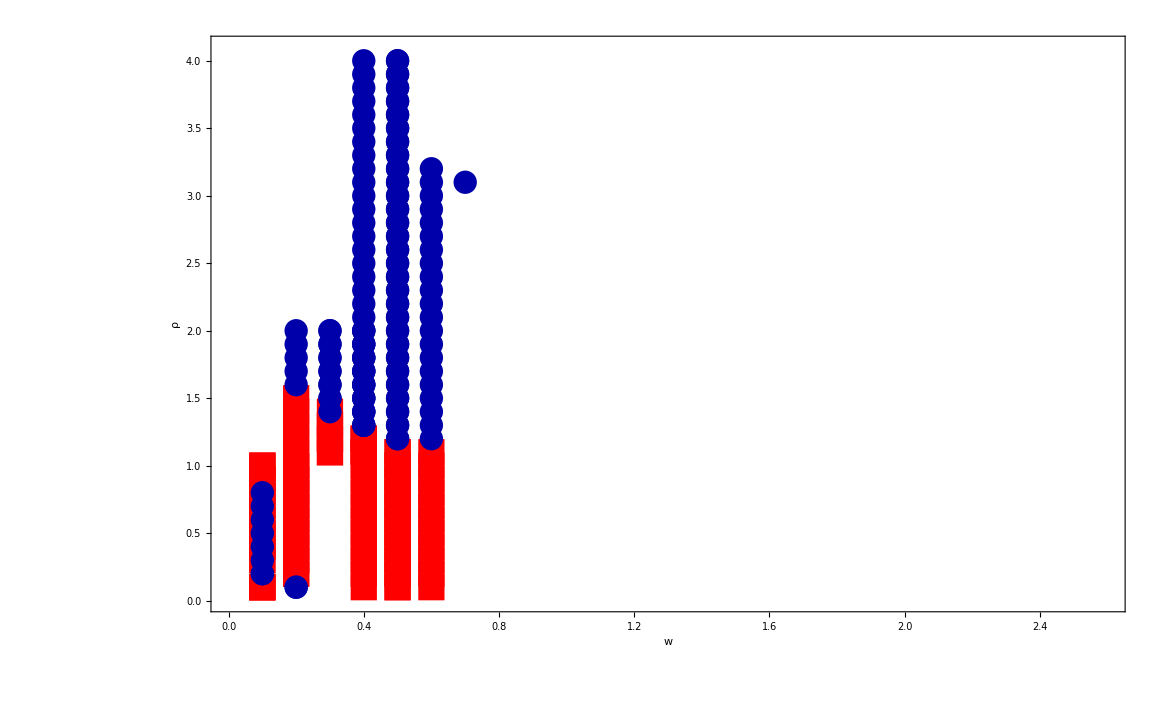

```mathematica
Show[{ListPlot[path,PlotStyle->Red,PlotMarkers->{Style["■",27]},PlotRange->{{0.0,2.6},{0.0,4.1}}],ListPlot[acc,PlotStyle->Darker[Blue],PlotMarkers->{Style["●",24]}]},Frame->True,FrameLabel->{Style["w",60],Style["ρ   ",60]},RotateLabel->False,LabelStyle->Directive[46,Black],FrameStyle->Thickness[0.003]]
```